```mathematica
(*Arbitraty dimension calcualtion*)
```

```mathematica
dim1=2;
vr1={t,x};
g1=L^2/Cos[x]^2({{-A[x] ⅇ^(-2δ[x]), 0}, {0, 1/A[x]}});
ω[t_,x_]:=Log[L Tan[x]]
sqdet1:=L^(d+1)/Cos[x]^(d+1)Sin[x]^(d-1)ⅇ^(-δ[x])
```

```mathematica
f1=FullSimplify[Inverse[g1]];
G1=FullSimplify[Table[Sum[1/2*f1[[i,l]]*(D[g1[[l,k]], vr1[[j]]]+D[g1[[l,j]], vr1[[k]]]-D[g1[[j,k]], vr1[[l]]]),{l,1,dim1}],{i,1,dim1},{j,1,dim1},{k,1,dim1}]];
Rm1=Simplify[Table[D[G1[[i,k,m]], vr1[[l]]]-D[G1[[i,k,l]], vr1[[m]]]+Sum[G1[[e,k,m]]*G1[[i,e,l]]-G1[[e,k,l]]*G1[[i,e,m]],{e,1,dim1}],{i,1,dim1},{k,1,dim1},{l,1,dim1},{m,1,dim1}]];
Rc1=FullSimplify[Table[Sum[Rm1[[i,k,i,m]],{i,1,dim1}],{k,1,dim1},{m,1,dim1}]];
R1=Simplify[Sum[Rc1[[i,j]]*f1[[i,j]],{i,1,dim1},{j,1,dim1}]];
Ge1=Simplify[Table[Rc1[[i,j]]-1/2*R1*g1[[i,j]],{i,1,dim1},{j,1,dim1}]];
```

```mathematica
D2[f_]:=Table[D[D[f, vr1[[j]]], vr1[[i]]]-Sum[G1[[k,i,j]]D[f, vr1[[k]]],{k,1,dim1}],{i,1,dim1},{j,1,dim1}]
DD[f_]:=Table[(D[f, vr1[[i]]])(D[f, vr1[[j]]]),{i,1,dim1},{j,1,dim1}]
```

```mathematica
D2Omega=Simplify[D2[ω[t,x]]];
DalOmega=Simplify[Tr[f1.D2Omega]];
DOmegaDOmega=Simplify[DD[ω[t,x]]];
DOmega2=Simplify[Tr[f1.DOmegaDOmega]];
```

```mathematica
GeTX=Simplify[Ge1-(d-1)(D2Omega+DOmegaDOmega)+g1((d-1) DalOmega+1/2 d(d-1)DOmega2-1/2(d-1)(d-2)ⅇ^(-2ω[t,x]))];
GeAng=Simplify[ⅇ^(2ω[t,x])((d-2) DalOmega+1/2(d-1)(d-2)DOmega2-1/2 R1)-1/2(d-2)(d-3)];
```

```mathematica
(*Subtracting vacuum energy*)
```

```mathematica
TeTX=Simplify[GeTX-(d(d-1))/(2 L^2)g1];
TeAng=Simplify[GeAng-(d(d-1))/(2 L^2)ⅇ^(2ω[t,x])];
```

```mathematica
(*Checking vanishing of Stress-Energy covariant derivative*)
```

```mathematica
FullSimplify[D[A[x]*TeTX[[2,2]],x]-(d-1)Csc[x]^3 Sec[x]TeAng+1/2 A[x] (2 (-3+2 d+Cos[2 x]) Csc[2 x]+A'[x]/A[x]-2 δ'[x])TeTX[[2,2]]+1/2 ⅇ^(2δ[x])/A[x] (2 Tan[x]+A'[x]/A[x]-2 δ'[x])TeTX[[1,1]]]
```

0

```mathematica
(*Matter part*)
```

```mathematica
(*Electro-Magnetic part*)
```

```mathematica
Aem1:={a[x],0}
```

```mathematica
Fem1 =Table[D[Aem1[[j]], vr1[[i]]]-D[Aem1[[i]], vr1[[j]]],{i,1,dim1},{j,1,dim1}];
Femup1=f1.Fem1.f1;
divAem1=Simplify[1/sqdet1 Sum[D[sqdet1 (f1.Aem1)[[ii]],vr1[[ii]]],{ii,1,dim1}]];
dFem1=Simplify[Table[1/sqdet1 Sum[D[sqdet1 Femup1[[ii,jj]],vr1[[ii]]],{ii,1,dim1}],{jj,1,dim1}].g1];
Lgr1em=Simplify[-1/4 Tr[Fem1.Femup1]];
Tem1=Simplify[Fem1.f1.(Transpose[Fem1])-g1 Lgr1em];
```

```mathematica
FullSimplify[dFem1[[1]]-(A[x] Cos[x]^2)/L^2(a''[x]+a'[x] (δ'[x]+(2 Cos[x]^2+d-3)/(Sin[x]Cos[x])))]
```

0

```mathematica
(*Scalar field part*)
```

```mathematica
$Assumptions={ϕ[x]∈ Reals,ϕ'[x]∈ Reals,t∈Reals,ω∈Reals,e∈Reals,a[x]∈Reals};
```

```mathematica
Φ[t_,x_]:=ϕ[x] ⅇ^(ⅈ ω t)
```

```mathematica
dPhi1=Simplify[Table[(D[Φ[t,x], vr1[[i]]]-ⅈ e Aem1[[i]]Φ[t,x]),{i,1,dim1}]];jcurr1=Simplify[Table[ⅈ e(Conjugate[Φ[t,x]]dPhi1[[ii]]-Conjugate[dPhi1[[ii]]]Φ[t,x]),{ii,1,dim1}]];
Lgr1phi=Simplify[dPhi1.f1.Conjugate[dPhi1]+V[Conjugate[Φ[t,x]] Φ[t,x]]];
TphiTX=FullSimplify[Table[Conjugate[dPhi1[[ii]]]dPhi1[[jj]]+dPhi1[[ii]]Conjugate[dPhi1[[jj]]]-
g1[[ii,jj]]Lgr1phi,{ii,1,dim1},{jj,1,dim1}]];
DalPhi1=FullSimplify[Sum[1/sqdet1 D[sqdet1 f1[[ii,jj]]D[Φ[t,x], vr1[[jj]]],vr1[[ii]]],{ii,1,dim1},{jj,1,dim1}]];
D2Phi1=FullSimplify[DalPhi1-2ⅈ e Sum[(Aem1.f1)[[ii]]D[Φ[t,x], vr1[[ii]]],{ii,1,dim1}]-ⅈ e divAem1 Φ[t,x]-e^2 Aem1.f1.Aem1 Φ[t,x]];
D2Phi1=Simplify[ⅇ^(-ⅈ ω t)D2Phi1];
```

```mathematica
TuTX=FullSimplify[(TphiTX+Tem1).f1];
EOMTX=TeTX-κ (TphiTX+Tem1);
EOMAng=TeAng+κ (Lgr1phi+Lgr1em)ⅇ^(2ω[t,x]);
```

```mathematica
(*Checking scalar field EOM*)
```

```mathematica
EOMPhi:=ϕ''[x]+(A'[x]/A[x]-δ'[x]+(d-1)/(Sin[x]Cos[x])) ϕ'[x]+1/A[x] (ⅇ^(2δ[x])/A[x](ω-e a[x])^2- L^2/Cos[x]^2 V'[ϕ[x]^2])ϕ[x] 
Simplify[L^2/(A[x] Cos[x]^2)(D2Phi1-V'[ϕ[x]^2]ϕ[x])-EOMPhi]
```

0

```mathematica
(*Checking electro-magnetic EOM*)
```

```mathematica
EOMEM:=a''[x]+a'[x] (δ'[x]+(2 Cos[x]^2+d-3)/(Sin[x]Cos[x]))+L^2/(A[x] Cos[x]^2)2 e (ω-e a[x]) ϕ[x]^2
Simplify[L^2/(A[x] Cos[x]^2)(dFem1[[1]]-jcurr1[[1]])-EOMEM]
```

0

```mathematica
(*Checking conservation consistency*)
```

```mathematica
FullSimplify[D[A[x]*EOMTX[[2,2]],x]-(d-1)Csc[x]^3 Sec[x]EOMAng+1/2 A[x] (2 (-3+2 d+Cos[2 x]) Csc[2 x]+A'[x]/A[x]-2 δ'[x])EOMTX[[2,2]]+1/2 ⅇ^(2δ[x])/A[x] (2 Tan[x]+A'[x]/A[x]-2 δ'[x])EOMTX[[1,1]]+2 A[x]ϕ'[x]κ EOMPhi-(ⅇ^(2 δ[x]) κ Cos[x]^2 a'[x])/L^2 EOMEM]
```

0

```mathematica
(*Gravitational equations*)
```

```mathematica
EOMA:=A'[x]+((A[x]-1) (d-2 Cos[x]^2))/(Sin[x]Cos[x])+(2 L^2 Tan[x])/(d-1)κ ρ[x]
EOMdelta:=δ'[x]+(L^2 Tan[x])/((d-1)A[x])κ(ρ[x]+pr[x])
```

```mathematica
A[x_]:=1-(2 L^2 κ)/(d-1)Cos[x]^2/Tan[x]^(d-2)∫_0^x Tan[x]^(d-1)/Cos[x]^2 ρ[x]ⅆx
```

```mathematica
FullSimplify[EOMA]
```

0

```mathematica
Clear[A]
```

```mathematica
Simplify[(TeTX.f1)[[1,1]]/.Solve[EOMA==0,A'[x]][[1]]]
FullSimplify[(TeTX.f1)[[2,2]]/.Solve[{EOMA==0,EOMdelta==0},{A'[x],δ'[x]}][[1]]]
```

-κ ρ[x]

κ pr[x]

```mathematica
(*Vacuum solutions*)
```

```mathematica
a[x_]:=(q L)/(d-2)(Cos[x]/Sin[x])^(d-2)
FullSimplify[a''[x]+a'[x] ((2 Cos[x]^2+d-3)/(Sin[x]Cos[x]))]
```

0

```mathematica
A[x_]:=1-(C[1] Cos[x]^2)/Tan[x]^(d-2)+(q^2 κ)/((d-1)(d-2)) Cos[x]^2/Tan[x]^(2d-4)
FullSimplify[EOMA/.ρ[x]->(Cos[x]^4 a'[x]^2)/(2 L^4),Assumptions->{d>0,x>0,x<π/2,L>0}]
```

0

```mathematica
ClearAll[A,a]
```

```mathematica
(*Special case d = 2*)
```

```mathematica
a[x_]:=q Log[Tan[x]]
FullSimplify[a''[x]+a'[x] ((2 Cos[x]^2+d-3)/(Sin[x]Cos[x]))/.d->2]
```

0

```mathematica
A[x_]:=1-C[1] Cos[x]^2-(q^2 κ)/L^2 Cos[x]^2 Log[Tan[x]]
FullSimplify[EOMA/.d->2/.ρ[x]->(Cos[x]^4 a'[x]^2)/(2 L^4)]
```

0

```mathematica
ClearAll[A,a]
```

```mathematica
(*Writing out full system*)
```

```mathematica
FullSimplify[ρ[x]+TuTX[[1,1]]/.ρ[x]->Cos[x]^2/L^2(ⅇ^(2 δ[x])/A[x] (ω-e a[x])^2 ϕ[x]^2+A[x] ϕ'[x]^2+(Cos[x]^2 ⅇ^(2 δ[x])a'[x]^2)/(2 L^2))+V[ϕ[x]^2]]
FullSimplify[pr[x]-TuTX[[2,2]]/.pr[x]->Cos[x]^2/L^2(ⅇ^(2 δ[x])/A[x] (ω-e a[x])^2  ϕ[x]^2+A[x] ϕ'[x]^2)-(Cos[x]^4 ⅇ^(2 δ[x])a'[x]^2)/(2 L^4)-V[ϕ[x]^2]]
```

0

0

```mathematica
FullSimplify[(2 Cos[x]^2)/L^2(ⅇ^(2 δ[x])/A[x] (ω-e a[x])^2 ϕ[x]^2+A[x] ϕ'[x]^2)-(ρ[x]+pr[x])/.{ρ[x]->Cos[x]^2/L^2(ⅇ^(2 δ[x])/A[x] (ω-e a[x])^2 ϕ[x]^2+A[x] ϕ'[x]^2+(Cos[x]^2 ⅇ^(2 δ[x])a'[x]^2)/(2 L^2))+V[ϕ[x]^2],pr[x]->Cos[x]^2/L^2(ⅇ^(2 δ[x])/A[x] (ω-e a[x])^2  ϕ[x]^2+A[x] ϕ'[x]^2)-(Cos[x]^4 ⅇ^(2 δ[x])a'[x]^2)/(2 L^4)-V[ϕ[x]^2]}]
Simplify[Cos[x]^2/L^2(ⅇ^(2 δ[x])/A[x] (ω-e a[x])^2  ϕ[x]^2-A[x] ϕ'[x]^2)+(Cos[x]^4 ⅇ^(2 δ[x])a'[x]^2)/(2 L^4)-V[ϕ[x]^2]+(Lgr1phi+Lgr1em)]
```

0

0

```mathematica
EOMA:=A'[x]+((A[x]-1) (d-2 Cos[x]^2))/(Sin[x]Cos[x])+κ(2Sin[x]Cos[x])/(d-1)(ⅇ^(2 δ[x])/A[x](ω-e a[x])^2 ϕ[x]^2+A[x] ϕ'[x]^2+(Cos[x]^2 ⅇ^(2 δ[x])a'[x]^2)/(2 L^2))+κ(2 L^2 Tan[x])/(d-1)V[ϕ[x]^2]
EOMdelta:=δ'[x]+κ(2Sin[x]Cos[x])/(d-1)(ⅇ^(2 δ[x])/A[x]^2(ω-e a[x])^2 ϕ[x]^2+ϕ'[x]^2)
```

```mathematica
FullSimplify[(EOMTX[[1,1]]/.Solve[EOMA==0,A'[x]][[1]]),Assumptions->{L>0}]
FullSimplify[(EOMTX[[2,2]]/.Solve[{EOMA==0,EOMdelta==0},{A'[x],δ'[x]}][[1]]),Assumptions->{L>0}]
```

0

0

```mathematica
(*3D and 4D Check*)
```

```mathematica
dim=4;
vr:={t,x,θ,ϕ}
g:=L^2/Cos[x]^2({{-A[x] ⅇ^(-2δ[x]), 0, 0, 0}, {0, 1/A[x], 0, 0}, {0, 0, Sin[x]^2, 0}, {0, 0, 0, Sin[x]^2 Sin[θ]^2}})
```

```mathematica
sqdet=Simplify[Sqrt[-Det[g]],Assumptions->{L>0,δ[x]>0,x>0,x<π/2,θ>0,θ<π} ];
```

```mathematica
f=FullSimplify[Inverse[g]];
G=FullSimplify[Table[Sum[1/2*f[[i,l]]*(D[g[[l,k]], vr[[j]]]+D[g[[l,j]], vr[[k]]]-D[g[[j,k]], vr[[l]]]),{l,1,dim}],{i,1,dim},{j,1,dim},{k,1,dim}]];
Rm=Simplify[Table[D[G[[i,k,m]], vr[[l]]]-D[G[[i,k,l]], vr[[m]]]+Sum[G[[e,k,m]]*G[[i,e,l]]-G[[e,k,l]]*G[[i,e,m]],{e,1,dim}],{i,1,dim},{k,1,dim},{l,1,dim},{m,1,dim}]];
Rc=FullSimplify[Table[Sum[Rm[[i,k,i,m]],{i,1,dim}],{k,1,dim},{m,1,dim}]];
R=Simplify[Sum[Rc[[i,j]]*f[[i,j]],{i,1,dim},{j,1,dim}]];
Ge=Simplify[Table[Rc[[i,j]]-1/2*R*g[[i,j]],{i,1,dim},{j,1,dim}]];
Geu=FullSimplify[Ge.f];
```

```mathematica
Te=Simplify[Ge-(d(d-1))/(2 L^2)g/.d->dim-1];
```

```mathematica
FullSimplify[Te[[1,1]]-TeTX[[1,1]]/.d->dim-1]
```

0

```mathematica
FullSimplify[Te[[2,2]]-TeTX[[2,2]]/.d->dim-1]
```

0

```mathematica
FullSimplify[Te[[3,3]]-TeAng/.d->dim-1]
```

0

```mathematica
(*Consistency check 4D*)
```

```mathematica
FullSimplify[D[A[x]*Te[[2,2]],x]-2 Csc[x]^3 Sec[x]Te[[3,3]]+1/2 A[x] (4 Cot[x]+2 Tan[x]+A'[x]/A[x]-2 δ'[x])Te[[2,2]]+1/2 ⅇ^(2δ[x])/A[x] (2 Tan[x]+A'[x]/A[x]-2 δ'[x])Te[[1,1]]]
```

0

```mathematica
(*Electromagnetic part*)
```

```mathematica
Aem={a[x],0,0,0};
```

```mathematica
Fem =Table[D[Aem[[j]], vr[[i]]]-D[Aem[[i]], vr[[j]]],{i,1,dim},{j,1,dim}];
Femup=f.Fem.f;
divAem=Simplify[1/sqdet Sum[D[sqdet (f.Aem)[[ii]],vr[[ii]]],{ii,1,dim}]];
dFem=Simplify[Table[Sum[1/sqdet D[sqdet Femup[[ii,jj]],vr[[ii]]],{ii,1,dim}],{jj,1,dim}].g];
Tem=Simplify[Fem.f.(Transpose[Fem])+1/4 g Tr[Fem.Femup]];
```

```mathematica
(*Scalar field part*)
```

```mathematica
$Assumptions={ϕ[x]∈ Reals,ϕ'[x]∈ Reals,t∈Reals,ω∈Reals,a[x]∈Reals,e∈Reals};
```

```mathematica
Φ[t_,x_]:=ϕ[x] ⅇ^(ⅈ ω t)
```

```mathematica
dPhi=Simplify[Table[(D[Φ[t,x], vr[[i]]]-ⅈ e Aem[[i]]Φ[t,x]),{i,1,dim}]];
dPhiconj=Refine[Table[Conjugate[dPhi[[i]]],{i,1,dim}]];
jcurr=Simplify[Table[ⅈ e(Conjugate[Φ[t,x]]dPhi[[i]]-dPhiconj[[i]]Φ[t,x]),{i,1,dim}]];
Lgr=Simplify[dPhi.f.dPhiconj+V[Conjugate[Φ[t,x]] Φ[t,x]]];
T=FullSimplify[Table[dPhiconj[[i]]dPhi[[j]]+dPhi[[i]]dPhiconj[[j]]-
g[[i,j]]Lgr,{i,1,dim},{j,1,dim}]];
DalPhi=FullSimplify[Sum[1/sqdet D[sqdet f[[ii,jj]]D[Φ[t,x], vr[[jj]]],vr[[ii]]],{ii,1,dim},{jj,1,dim}]];
D2Phi=FullSimplify[DalPhi-2ⅈ e Sum[(Aem.f)[[ii]]D[Φ[t,x], vr[[ii]]],{ii,1,dim}]-ⅈ e divAem Φ[t,x]-e^2 Aem.f.Aem Φ[t,x]];
D2Phi=Simplify[ⅇ^(-ⅈ ω t)D2Phi];
```

```mathematica
Simplify[L^2/(A[x] Cos[x]^2)(D2Phi-V'[ϕ[x]^2]ϕ[x])-EOMPhi/.d->dim-1]
```

0

```mathematica
Tu=FullSimplify[(T+Tem).f];
```

```mathematica
Simplify[Cos[x]^2/L^2(1/A[x] ⅇ^(2 δ[x])(ω-e a[x])^2 ϕ[x]^2+A[x] ϕ'[x]^2)+(Cos[x]^4 ⅇ^(2 δ[x])a'[x]^2)/(2 L^4)+V[ϕ[x]^2]+Tu[[1,1]]]
Simplify[Cos[x]^2/L^2(ⅇ^(2 δ[x])/A[x] (ω-e a[x])^2  ϕ[x]^2+A[x] ϕ'[x]^2)-(Cos[x]^4 ⅇ^(2 δ[x])a'[x]^2)/(2 L^4)-V[ϕ[x]^2]-Tu[[2,2]]]
Simplify[Cos[x]^2/L^2(ⅇ^(2 δ[x])/A[x] (ω-e a[x])^2  ϕ[x]^2-A[x] ϕ'[x]^2)+(Cos[x]^4 ⅇ^(2 δ[x])a'[x]^2)/(2 L^4)-V[ϕ[x]^2]-Tu[[3,3]]]
```

0

0

0

```mathematica
Simplify[dFem-jcurr/.Solve[EOMEM==0,a''[x]][[1]]/.d->dim-1]
```

{0,0,0,0}

```mathematica
(*Scalar field exact solution with no backreaction*)
```

```mathematica
FieldEOM[f_]:=D[f,{x,2}]+(d-1)/(Sin[x]Cos[x])D[f,x]+(ω^2- (m^2 L^2)/Cos[x]^2)f
```

```mathematica
e[j_,x_]:=Cos[x]^d JacobiP[j,d/2-1,d/2,Cos[2x]]
```

```mathematica
FullSimplify[(FieldEOM[e[j,x]]/.ω->(d+2j)/.m->0)/.j->5]
```

0

```mathematica
ClearAll[ω]
```

```mathematica
DSolve[FieldEOM[F[x]]==0,F[x],x]
```

{{F[x]→(-1)^(1/4 (d-√(d^2+4 L^2 m^2))) C[1] Cos[x]^(1/2 (d-√(d^2+4 L^2 m^2))) Hypergeometric2F1[d/4-1/4 √(d^2+4 L^2 m^2)-ω/2,d/4-1/4 √(d^2+4 L^2 m^2)+ω/2,1-1/2 √(d^2+4 L^2 m^2),Cos[x]^2]+(-1)^(1/4 (d+√(d^2+4 L^2 m^2))) C[2] Cos[x]^(1/2 (d+√(d^2+4 L^2 m^2))) Hypergeometric2F1[d/4+1/4 √(d^2+4 L^2 m^2)-ω/2,d/4+1/4 √(d^2+4 L^2 m^2)+ω/2,1+1/2 √(d^2+4 L^2 m^2),Cos[x]^2]}}

```mathematica
(*A singular branch*)
```

```mathematica
Assuming[d>0,Refine[Cos[x]^(1/2 (d-√(d^2+4 L^2 m^2))) Hypergeometric2F1[d/4-1/4 √(d^2+4 L^2 m^2)-ω/2,d/4-1/4 √(d^2+4 L^2 m^2)+ω/2,1-1/2 √(d^2+4 L^2 m^2),Cos[x]^2]/.m->0]]
```

Hypergeometric2F1[-ω/2,ω/2,1-d/2,Cos[x]^2]

```mathematica
(*Considering regular branch*)
```

```mathematica
Assuming[d>0,Refine[Cos[x]^(1/2 (d+√(d^2+4 L^2 m^2))) Hypergeometric2F1[d/4+1/4 √(d^2+4 L^2 m^2)-ω/2,d/4+1/4 √(d^2+4 L^2 m^2)+ω/2,1+1/2 √(d^2+4 L^2 m^2),Cos[x]^2]/.m->0]]
```

Cos[x]^d Hypergeometric2F1[d/2-ω/2,d/2+ω/2,1+d/2,Cos[x]^2]

```mathematica
Clear[ω,a,b,c,p]
```

```mathematica
a:=d/4+1/4 √(d^2+4 L^2 m^2)-ω/2
b:=d/4+1/4 √(d^2+4 L^2 m^2)+ω/2
c:=1+1/2 √(d^2+4 L^2 m^2)
p:=1/2 (d+√(d^2+4 L^2 m^2))
```

```mathematica
(*(Gamma[c]Gamma[c-a-b])/(Gamma[c-a]Gamma[c-b])Hypergeometric2F1[a,b,a+b+1-c,Sin[x]^2]+(Gamma[c]Gamma[a+b-c])/(Gamma[a]Gamma[b])Sin[x]^(2(c-a-b))Hypergeometric2F1[c-a,c-b,c+1-a-b,Sin[x]^2]*)
```

```mathematica
p:=1/2 (d+√(d^2+4 L^2 m^2))
ω:=p+2j
```

```mathematica
Func[x_]:=Cos[x]^p Hypergeometric2F1[-j,p+j,d/2,Sin[x]^2]
FullSimplify[FieldEOM[Func[x]]/.j->6]
```

0

```mathematica
Func[x_]:=Cos[x]^(d/2+1/2 √(d^2+4 L^2 m^2))JacobiP[j,d/2-1,1/2 √(d^2+4 L^2 m^2),Cos[2x]]
FullSimplify[FieldEOM[Func[x]]/.j->6]
```

0

```mathematica
(*Plotting*)
```

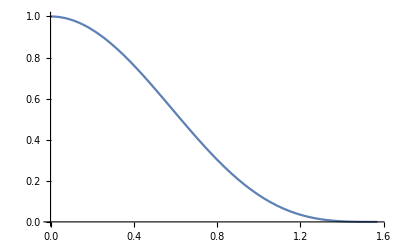

```mathematica
Plot[Cos[x]^(d/2+1/2 √(d^2+4 L^2 m^2)) JacobiP[j,d/2-1,1/2 √(d^2+4 L^2 m^2),Cos[2x]]/.j->0/.d->3/.m->1/.L->1,{x,0,π/2},PlotRange->All]
```